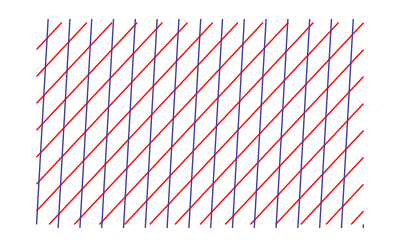

```mathematica
α1=30;

α2=2;
span = 30;
Show[{Plot[Tan[(90-α1) π/180]x+#&/@Range[-50,30,4],{x,0,span},Axes->False,PlotStyle->Red,PlotRange->{{0,span},{0,span}}],
Plot[Tan[(90-α2)π/180](x-#)&/@Range[0,30,2],{x,0,span}]
}]
```